# ANALIZA PREPOVEDANIH DROG V SLOVENIJI

## Pridobivanje podatkov

```mathematica
podatkiCENA = Import["C:\\Users\\Lara\\Desktop\\ROM seminarska\\cene.xlsx"];
cistostInKakovot = Import["C:\\Users\\Lara\\Desktop\\ROM seminarska\\čistost in kakovost prepovedanih drog.xlsx"];
porabljenaSredstva = Import["C:\\Users\\Lara\\Desktop\\ROM seminarska\\porabljena sredstva.xlsx"];
obravnavaniBolniki = Import["C:\\Users\\Lara\\Desktop\\ROM seminarska\\Število obravnavanih bolnikov zaradi.xlsx"];
stUmrlih = Import["C:\\Users\\Lara\\Desktop\\ROM seminarska\\število umrlih po letih.xlsx"];
štZasegov = Import["C:\\Users\\Lara\\Desktop\\ROM seminarska\\število zasegov.xlsx"];
```

## Porabljena sredstva za področje drog

### Vsa porabljena sredstva na leto

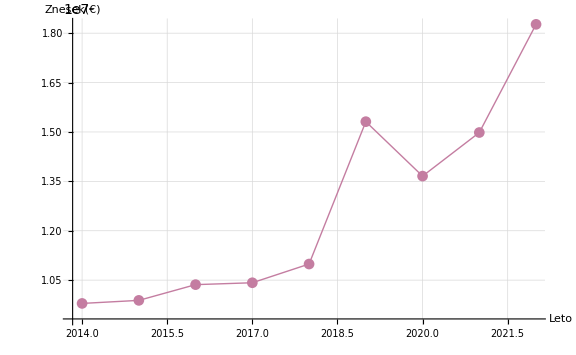
LETO | ZNESEK (€)
2022. | 18268766.53
2021. | 14983291.02
2020. | 13659558.11
2019. | 15312915.02
2018. | 10988926.43
2017. | 10420376.85
2016. | 10363172.18
2015. | 9885113.03
2014. | 9792506.96-Graphics-

```mathematica
vsa = porabljenaSredstva[[10]];
podatkivsa = Prepend[vsa,{"LETO", "ZNESEK (€)"}];

tabvse = Grid[
MapAt[
AccountingForm[#, {Infinity, 2}]&,
podatkivsa,
{2;;, 2}
],
Frame->All,
Alignment->Center,
ItemStyle->{Directive[FontFamily->"Arial"], None},
ItemSize->{10, 2},
Background->{None, {{RGBColor[0.77,0.49,0.63], None}}}
];

leta =vsa[[1;;,1]];
zneski = vsa[[1;;,2]];
grafvse = ListLinePlot[Transpose[{leta, zneski}],
PlotMarkers->Automatic,
PlotStyle->{Thick, RGBColor[0.77,0.49,0.63]},
AxesLabel->{"Leto", "Znesek(€)"},
GridLines -> Automatic,
ImageSize->Large];

Row[{tabvse, Spacer[100], grafvse}]
```

### Občine

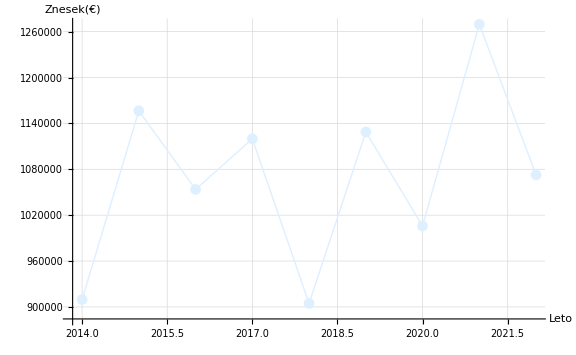
-Graphics- LETO | ZNESEK (€)
2022. | 1072672.04
2021. | 1269576.26
2020. | 1005857.61
2019. | 1128724.73
2018. | 904567.32
2017. | 1119854.87
2016. | 1053687.99
2015. | 1156493.85
2014. | 909629.72

```mathematica
občine = porabljenaSredstva[[1]];
podatkiObčina = Prepend[občine,{"LETO", "ZNESEK (€)"}];

tabob = Grid[
MapAt[
AccountingForm[#, {Infinity, 2}]&,
podatkiObčina,
{2;;, 2}
],
Frame->All,
Alignment->Center,
ItemStyle->{Directive[FontFamily->"Arial"], None},
ItemSize->{10, 2},
Background->{None, {{LightBlue, None}}}
];
znesekobčina = občine[[1;;,2]];
grafob = ListLinePlot[Transpose[{leta, znesekobčina}],
PlotMarkers->Automatic,
PlotStyle->{Thick, LightBlue},
AxesLabel->{"Leto", "Znesek(€)"},
GridLines -> Automatic,
ImageSize->Large];
tabob grafob
```

### FIHO

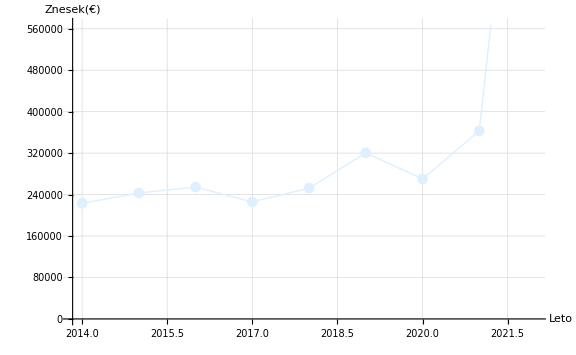
-Graphics- LETO | ZNESEK (€)
2022. | 1368807.87
2021. | 362957.87
2020. | 270143.99
2019. | 320492.01
2018. | 252448.92
2017. | 225865.3
2016. | 254483.4
2015. | 243079.78
2014. | 223259.74

```mathematica
FIHO = porabljenaSredstva[[2]];
podatkiFIHO= Prepend[FIHO,{"LETO", "ZNESEK (€)"}];

tabFIHO =Grid[
MapAt[
AccountingForm[#, {Infinity, 2}]&,
podatkiFIHO,
{2;;, 2}
],
Frame->All,
Alignment->Center,
ItemStyle->{Directive[FontFamily->"Arial"], None},
ItemSize->{10, 2},
Background->{None, {{LightBlue, None}}}
];
znesekFIHO = FIHO[[1;;,2]];
grafFIHO = ListLinePlot[Transpose[{leta, znesekFIHO}],
PlotMarkers->Automatic,
PlotStyle->{Thick, LightBlue},
AxesLabel->{"Leto", "Znesek(€)"},
GridLines -> Automatic,
ImageSize->Large];
grafFIHO tabFIHO
```

### Urad za mlade

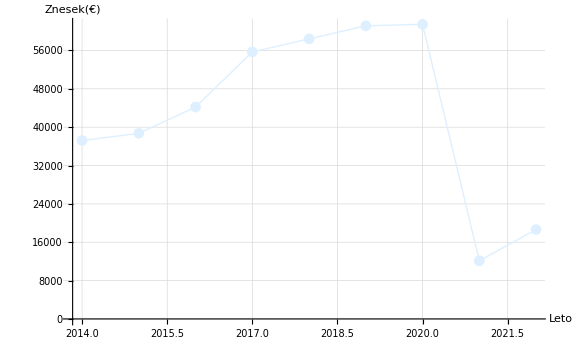
-Graphics- LETO | ZNESEK (€)
2022. | 18650.
2021. | 12125.
2020. | 61450.
2019. | 61145.
2018. | 58416.
2017. | 55687.
2016. | 44199.
2015. | 38718.
2014. | 37207.5

```mathematica
Urad = porabljenaSredstva[[3]];
podatkiUrad= Prepend[Urad,{"LETO", "ZNESEK (€)"}];

taburad = Grid[
MapAt[
AccountingForm[#, {Infinity, 2}]&,
podatkiUrad,
{2;;, 2}
],
Frame->All,
Alignment->Center,
ItemStyle->{Directive[FontFamily->"Arial"], None},
ItemSize->{10, 2},
Background->{None, {{LightBlue, None}}}
];
znesekurad = Urad[[1;;,2]];
grafurad= ListLinePlot[Transpose[{leta, znesekurad}],
PlotMarkers->Automatic,
PlotStyle->{Thick, LightBlue},
AxesLabel->{"Leto", "Znesek(€)"},
GridLines -> Automatic,
ImageSize->Large];
grafurad taburad
```

### ZZZS

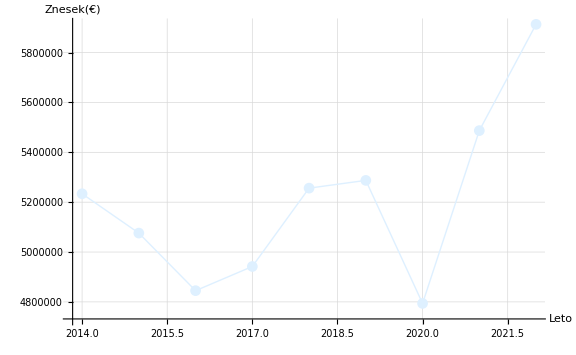
-Graphics- LETO | ZNESEK (€)
2022. | 5913554.
2021. | 5487140.
2020. | 4793799.
2019. | 5287441.
2018. | 5256370.
2017. | 4942000.
2016. | 4845000.
2015. | 5076000.
2014. | 5233791.

```mathematica
ZZZS = porabljenaSredstva[[4]];
podatkiZZZS= Prepend[ZZZS,{"LETO", "ZNESEK (€)"}];

tabZZZS = Grid[
MapAt[
AccountingForm[#, {Infinity, 2}]&,
podatkiZZZS,
{2;;, 2}
],
Frame->All,
Alignment->Center,
ItemStyle->{Directive[FontFamily->"Arial"], None},
ItemSize->{10, 2},
Background->{None, {{LightBlue, None}}}
];
zneseZZZS = ZZZS[[1;;,2]];
grafZZZS= ListLinePlot[Transpose[{leta, zneseZZZS}],
PlotMarkers->Automatic,
PlotStyle->{Thick, LightBlue},
AxesLabel->{"Leto", "Znesek(€)"},
GridLines -> Automatic,
ImageSize->Large];
grafZZZS tabZZZS
```

### ZZZS varno iniciranje drog

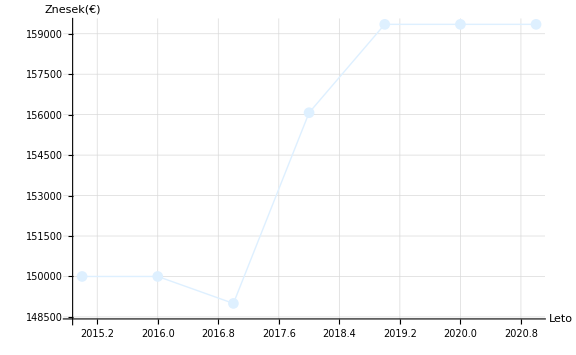
-Graphics- LETO | ZNESEK (€)
2021. | 159349.
2020. | 159349.
2019. | 159349.
2018. | 156072.
2017. | 149000.
2016. | 150000.
2015. | 150000.

```mathematica
ZZZSv = porabljenaSredstva[[5]];
podatkiZZZSv= Prepend[ZZZSv,{"LETO", "ZNESEK (€)"}];

tabZZZSv = Grid[
MapAt[
AccountingForm[#, {Infinity, 2}]&,
podatkiZZZSv,
{2;;, 2}
],
Frame->All,
Alignment->Center,
ItemStyle->{Directive[FontFamily->"Arial"], None},
ItemSize->{10, 2},
Background->{None, {{LightBlue, None}}}
];
letoZZZSv = ZZZSv[[1;;,1]];
zneseZZZSv = ZZZSv[[1;;,2]];
grafZZZSv= ListLinePlot[Transpose[{letoZZZSv, zneseZZZSv}],
PlotMarkers->Automatic,
PlotStyle->{Thick, LightBlue},
AxesLabel->{"Leto", "Znesek(€)"},
GridLines -> Automatic,
ImageSize->Large];
grafZZZSv tabZZZSv
```

### MZ

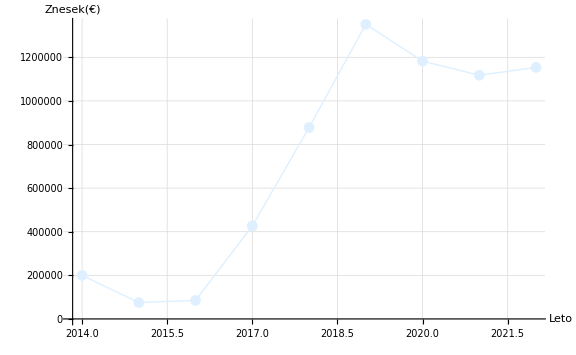
{{Null},{Null^2 -Graphics- LETO | ZNESEK (€)
2022. | 1153548.6
2021. | 1117676.5
2020. | 1182426.17
2019. | 1351196.72
2018. | 878028.
2017. | 426428.
2016. | 85000.
2015. | 75000.
2014. | 200000.}}

```mathematica
MZ = porabljenaSredstva[[6]];
podatkiMZ= Prepend[MZ,{"LETO", "ZNESEK (€)"}];

{{tabMZ = Grid[
MapAt[
AccountingForm[#, {Infinity, 2}]&,
podatkiMZ,
{2;;, 2}
],
Frame->All,
Alignment->Center,
ItemStyle->{Directive[FontFamily->"Arial"], None},
ItemSize->{10, 2},
Background->{None, {{LightBlue, None}}}
];}, {zneseMZ = MZ[[1;;,2]];
grafMZ= ListLinePlot[Transpose[{leta, zneseMZ}],
PlotMarkers->Automatic,
PlotStyle->{Thick, LightBlue},
AxesLabel->{"Leto", "Znesek(€)"},
GridLines -> Automatic,
ImageSize->Large];
grafMZ tabMZ}}
```

### MDDSZEM

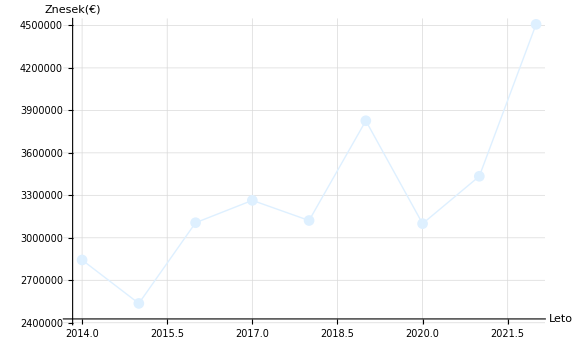
-Graphics- LETO | ZNESEK (€)
2022. | 4507717.9
2021. | 3434576.
2020. | 3100000.
2019. | 3826796.23
2018. | 3122159.
2017. | 3264467.
2016. | 3106617.
2015. | 2536541.
2014. | 2843425.

```mathematica
MDDSZEM = porabljenaSredstva[[7]];
podatkiMDDSZEM= Prepend[MDDSZEM,{"LETO", "ZNESEK (€)"}];

tabMDDSZEM = Grid[
MapAt[
AccountingForm[#, {Infinity, 2}]&,
podatkiMDDSZEM,
{2;;, 2}
],
Frame->All,
Alignment->Center,
ItemStyle->{Directive[FontFamily->"Arial"], None},
ItemSize->{10, 2},
Background->{None, {{LightBlue, None}}}
];
zneseMDDSZEM = MDDSZEM[[1;;,2]];
grafMZ= ListLinePlot[Transpose[{leta, zneseMDDSZEM}],
PlotMarkers->Automatic,
PlotStyle->{Thick, LightBlue},
AxesLabel->{"Leto", "Znesek(€)"},
GridLines -> Automatic,
ImageSize->Large];
grafMZ tabMDDSZEM
```

### MNZ

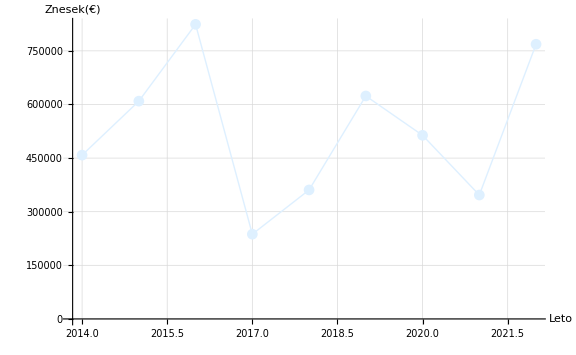
-Graphics- LETO | ZNESEK (€)
2022. | 768485.27
2021. | 346646.39
2020. | 513700.34
2019. | 623808.33
2018. | 360864.9
2017. | 237073.98
2016. | 824184.79
2015. | 609280.4
2014. | 458249.

```mathematica
MNZ = porabljenaSredstva[[8]];
podatkiMNZ= Prepend[MNZ,{"LETO", "ZNESEK (€)"}];

tabMNZ=Grid[
MapAt[
AccountingForm[#, {Infinity, 2}]&,
podatkiMNZ,
{2;;, 2}
],
Frame->All,
Alignment->Center,
ItemStyle->{Directive[FontFamily->"Arial"], None},
ItemSize->{10, 2},
Background->{None, {{LightBlue, None}}}
];
zneseMNZ = MNZ[[1;;,2]];
grafMNZ= ListLinePlot[Transpose[{leta, zneseMNZ}],
PlotMarkers->Automatic,
PlotStyle->{Thick, LightBlue},
AxesLabel->{"Leto", "Znesek(€)"},
GridLines -> Automatic,
ImageSize->Large];
grafMNZ tabMNZ
```

### Univerzitetna psihiatrična klinika Ljubljana

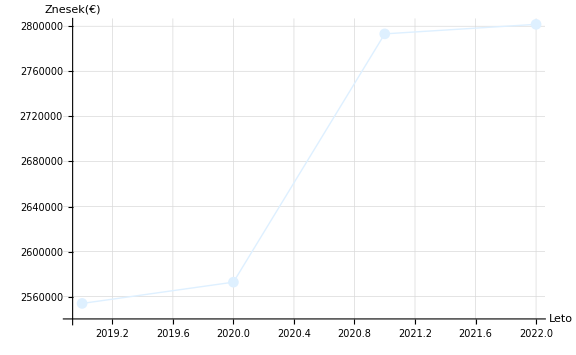
-Graphics- LETO | ZNESEK (€)
2022. | 2801699.
2021. | 2793244.
2020. | 2572832.
2019. | 2553962.

```mathematica
klinika= porabljenaSredstva[[9]];
podatkiklinika= Prepend[klinika,{"LETO", "ZNESEK (€)"}];

tabuni=Grid[
MapAt[
AccountingForm[#, {Infinity, 2}]&,
podatkiklinika,
{2;;, 2}
],
Frame->All,
Alignment->Center,
ItemStyle->{Directive[FontFamily->"Arial"], None},
ItemSize->{10, 2},
Background->{None, {{LightBlue, None}}}
];
zneseuni = klinika[[1;;,2]];
letouni =klinika[[1;;,1]];
grafuni= ListLinePlot[Transpose[{letouni, zneseuni}],
PlotMarkers->Automatic,
PlotStyle->{Thick, LightBlue},
AxesLabel->{"Leto", "Znesek(€)"},
GridLines -> Automatic,
ImageSize->Large];
grafuni tabuni
```

## Število obravnavanih oseb zaradi zastrupitev s prepovedanimi drogami v UKC Ljubljana, 2010 – 2022

### Število vseh obravnavanih bolnikov

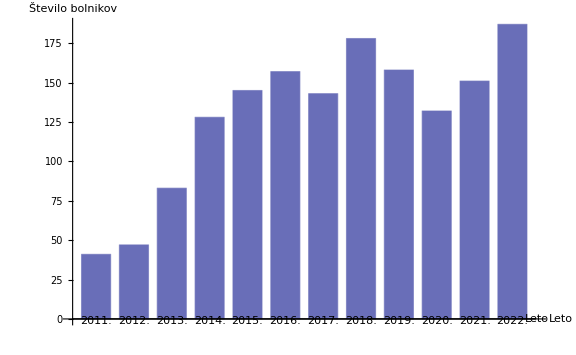

```mathematica
obravnavaniVsi = obravnavaniBolniki[[2]];
letoObravnave = obravnavaniVsi[[2;;,1]];
številoBolnikov = obravnavaniVsi[[2;;,2]];

BarChart[številoBolnikov,
AxesLabel-> {"Leto", "Število bolnikov"},
ChartStyle->RGBColor[0.41,0.43,0.72],
BarSpacing->0.3,
ChartLabels->{Placed[letoObravnave, Axis]},
ImageSize->Large
]
```

### Število obravnanvanih zaradi zastrupitve zaradi kokaina in heroina

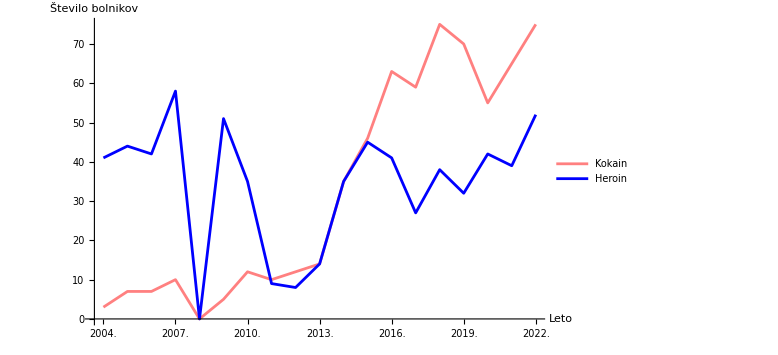

```mathematica
HeroKoka = obravnavaniBolniki[[1]];
ListLinePlot[{HeroKoka[[All, {1,2}]], HeroKoka[[All, {1,3}]]},
PlotStyle->{Pink, Blue},
PlotLegends->{"Kokain", "Heroin"},
AxesLabel->{"Leto", "Število bolnikov"},
ImageSize->Large,
Ticks->{HeroKoka[[All, 1]], Automatic}]
```

## Centrov za preprečevanje in zdravljenje odvisnosti od prepovedanih drog (CPZOPD)

```mathematica
GeoGraphics[{GeoStyling["StreetMap"], Polygon[Entity["Country","Slovenia"]], GeoMarker[Entity["City",{"Ljubljana","Osrednjeslovenska","Slovenia"}]],GeoMarker[Entity["City",{"MurskaSobota","Pomurska","Slovenia"}]], GeoMarker[Entity["City",{"Kranj","Gorenjska","Slovenia"}]], GeoMarker[Entity["City",{"Logatec","Osrednjeslovenska","Slovenia"}]], GeoMarker[Entity["City",{"NovaGorica","Goriska","Slovenia"}]], GeoMarker[Entity["AdministrativeDivision",{"Sezana","Slovenia"}]], GeoMarker[Entity["City",{"Koper","ObalnoKraska","Slovenia"}]], GeoMarker[Entity["City",{"Pivka","NotranjskoKraska","Slovenia"}]], GeoMarker[Entity["City",{"IlirskaBistrica","NotranjskoKraska","Slovenia"}]], GeoMarker[Entity["AdministrativeDivision",{"Kocvevje","Slovenia"}]], GeoMarker[Entity["City",{"NovoMesto","JugovzodnaSlovenija","Slovenia"}]], GeoMarker[Entity["AdministrativeDivision",{"Brezice","Slovenia"}]], GeoMarker[Entity["City",{"Trbovlje","Zasavska","Slovenia"}]], GeoMarker[Entity["City",{"Celje","Savinjska","Slovenia"}]], GeoMarker[Entity["City",{"Velenje","Savinjska","Slovenia"}]], GeoMarker[Entity["City",{"SlovenjGradec","Koroska","Slovenia"}]], GeoMarker[Entity["City",{"Maribor","Podravska","Slovenia"}]], GeoMarker[Entity["AdministrativeDivision",{"Ptuj","Slovenia"}]], GeoMarker[]},
GeoBackground->None
]
```

-Graphics-

## Število umrilh po starostnih skupinah

### Število umrih v letu 2022

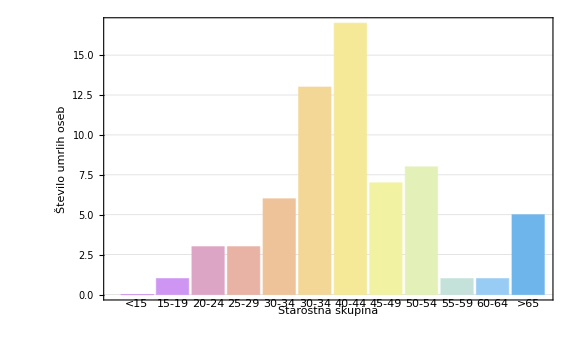

```mathematica
leto22 = stUmrlih[[1]];
starosSkup22 = leto22[[All, 1]];
steviloOseb22 = leto22[[All, 2]];

BarChart[steviloOseb22,
ChartLabels->Placed[starosSkup22, Below],
ChartStyle->"Pastel",
BarSpacing->0.1,
AxesLabel->{"Starostna skupina", "Število umrlih oseb"},
ImageSize->Large,
PlotTheme->"Detailed"
]
```

### Število umrlih v letu 2021

```mathematica
leto21 = stUmrlih[[2]];
starosSkup21 = leto21[[All, 1]];
steviloOseb21 = leto21[[All, 2]];

BarChart[steviloOseb21,
ChartLabels->Placed[starosSkup21, Below],
ChartStyle->"Pastel",
BarSpacing->0.1,
AxesLabel->{"Starostna skupina", "Število umrlih oseb"},
ImageSize->Large,
PlotTheme->"Detailed"
]
```

-Graphics-

### Število umrlih v letu 2019

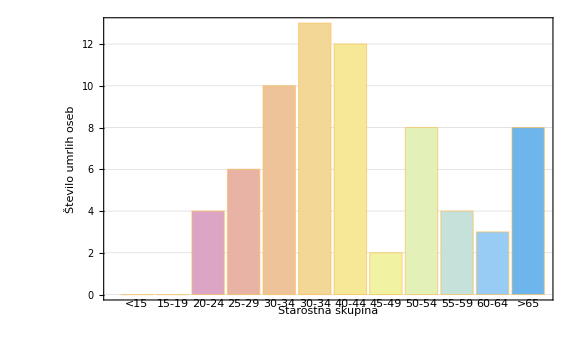
-Graphics--Graphics-

```mathematica
leto19 = stUmrlih[[3]];
starosSkup19 = leto19[[All, 1]];
steviloOseb19 = leto19[[All, 2]];

graf19= BarChart[steviloOseb19,
ChartLabels->Placed[starosSkup19, Below],
ChartStyle->"Pastel",
BarSpacing->0.1,
AxesLabel->{"Starostna skupina", "Število umrlih oseb"},
ImageSize->Large,
PlotTheme->"Detailed"
];
torti19 = PieChart[{14,86}, 
ChartLabels-> Placed[{"14%", "86%"}, "RadialCallout"],
ChartLegends->{"Ženske", "Moški"}, 
 ChartStyle->{LightPink, LightBlue},
ImageSize->Medium
];
Row[{graf19, Spacer[100], torti19}]
```

### Število umrlih v letu 2018

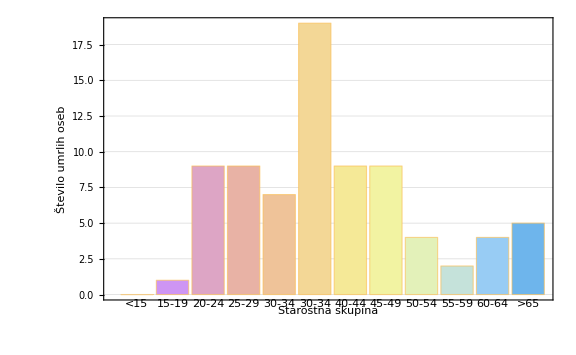
-Graphics--Graphics-

```mathematica
leto18 = stUmrlih[[4]];
starosSkup18 = leto18[[All, 1]];
steviloOseb18 = leto18[[All, 2]];

graf18=BarChart[steviloOseb18,
ChartLabels->Placed[starosSkup18, Below],
ChartStyle->"Pastel",
BarSpacing->0.1,
AxesLabel->{"Starostna skupina", "Število umrlih oseb"},
ImageSize->Large,
PlotTheme->"Detailed"
];
torti18 = PieChart[{19,81}, 
ChartLabels-> Placed[{"19%", "81%"}, "RadialCallout"],
ChartLegends->{"Ženske", "Moški"}, 
 ChartStyle->{LightPink, LightBlue},
ImageSize->Medium
];
Row[{graf18, Spacer[100], torti18}]
```

### Število umrlih v letu 2017

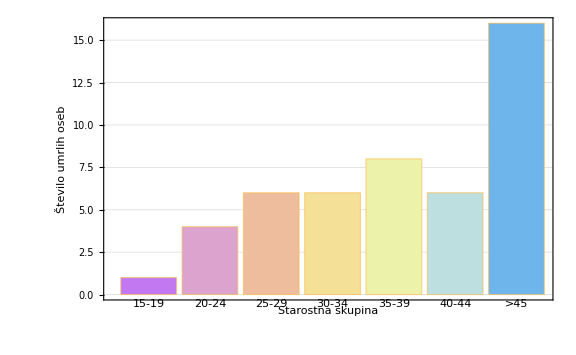
-Graphics--Graphics-

```mathematica
leto17 = stUmrlih[[5]];
starosSkup17 = leto17[[All, 1]];
steviloOseb17 = leto17[[All, 2]];

graf17=BarChart[steviloOseb17,
ChartLabels->Placed[starosSkup17, Below],
ChartStyle->"Pastel",
BarSpacing->0.1,
AxesLabel->{"Starostna skupina", "Število umrlih oseb"},
ImageSize->Large,
PlotTheme->"Detailed"
];
torti17 = PieChart[{21,79}, 
ChartLabels-> Placed[{"21%", "79%"}, "RadialCallout"],
ChartLegends->{"Ženske", "Moški"}, 
 ChartStyle->{LightPink, LightBlue},
ImageSize->Medium,
PlotLabel->"Delež umrlih po spolu"
];
Row[{graf17, Spacer[100], torti17}]
```

### Število umrlih v letu 2016

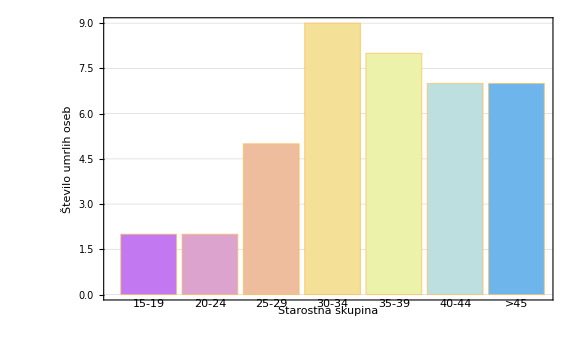
-Graphics--Graphics-

```mathematica
leto16 = stUmrlih[[6]];
starosSkup16 = leto16[[All, 1]];
steviloOseb16 = leto16[[All, 2]];

graf16=BarChart[steviloOseb16,
ChartLabels->Placed[starosSkup16, Below],
ChartStyle->"Pastel",
BarSpacing->0.1,
AxesLabel->{"Starostna skupina", "Število umrlih oseb"},
ImageSize->Large,
PlotTheme->"Detailed"
];
torti16 = PieChart[{13,87}, 
ChartLabels-> Placed[{"13%", "87%"}, "RadialCallout"],
ChartLegends->{"Ženske", "Moški"}, 
 ChartStyle->{LightPink, LightBlue},
ImageSize->Medium,
PlotLabel->"Delež umrlih po spolu"
];
Row[{graf16, Spacer[100], torti16}]
```

### Število umrlih v letu 2015

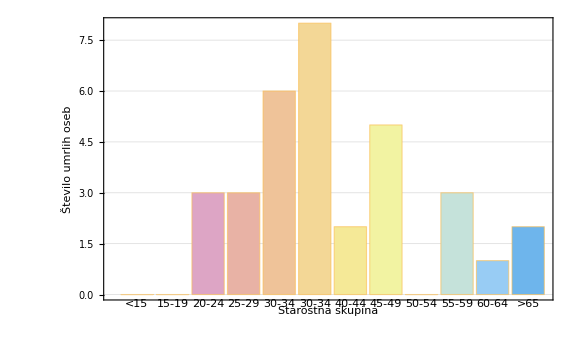
-Graphics--Graphics-

```mathematica
leto15 = stUmrlih[[7]];
starosSkup15 = leto15[[All, 1]];
steviloOseb15 = leto15[[All, 2]];

graf15=BarChart[steviloOseb15,
ChartLabels->Placed[starosSkup15, Below],
ChartStyle->"Pastel",
BarSpacing->0.1,
AxesLabel->{"Starostna skupina", "Število umrlih oseb"},
ImageSize->Large,
PlotTheme->"Detailed"
];
torti15 = PieChart[{12.5,87.5}, 
ChartLabels-> Placed[{"12,5%", "87,5%"}, "RadialCallout"],
ChartLegends->{"Ženske", "Moški"}, 
 ChartStyle->{LightPink, LightBlue},
ImageSize->Medium
];
Row[{graf15, Spacer[100], torti15 }]
```

### Število umrlih v letu 2014

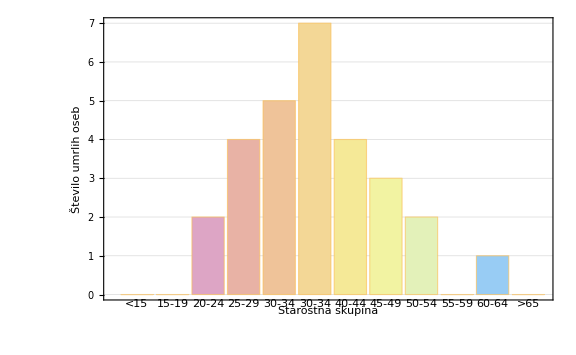
-Graphics--Graphics-

```mathematica
leto14 = stUmrlih[[8]];
starosSkup14= leto14[[All, 1]];
steviloOseb14= leto14[[All, 2]];

graf14=BarChart[steviloOseb14,
ChartLabels->Placed[starosSkup14, Below],
ChartStyle->"Pastel",
BarSpacing->0.1,
AxesLabel->{"Starostna skupina", "Število umrlih oseb"},
ImageSize->Large,
PlotTheme->"Detailed"
];
torti14 = PieChart[{7.1,92.9}, 
ChartLabels-> Placed[{"7,1%", "92,9%"}, "RadialCallout"],
ChartLegends->{"Ženske", "Moški"}, 
 ChartStyle->{LightPink, LightBlue},
ImageSize->Medium
];
Row[{graf14, Spacer[100], torti14  }]
```

## Cene v EUR po posameznih prepovedanih drogah na drobno

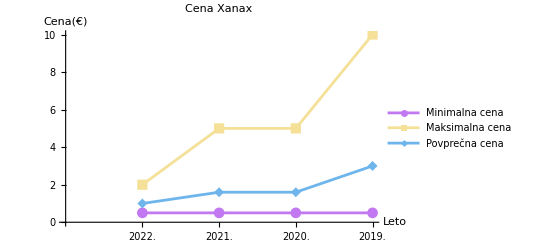
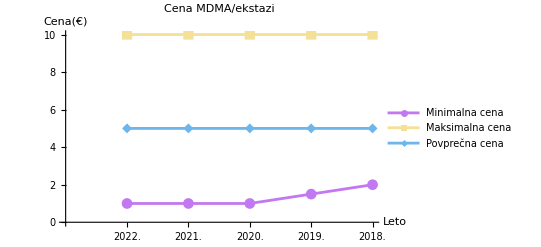
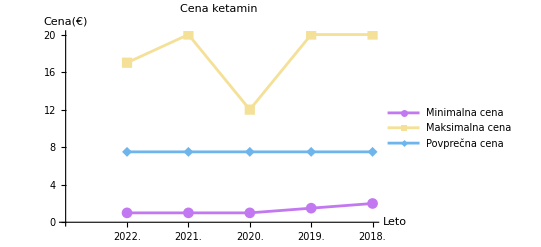
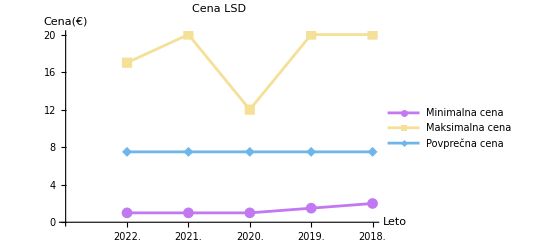
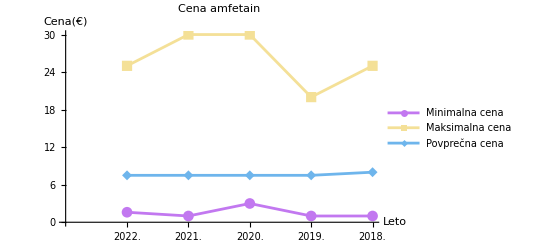
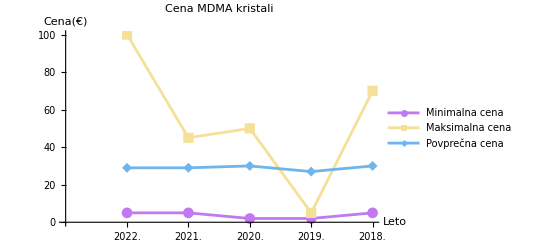
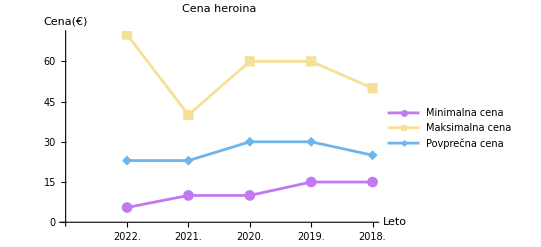
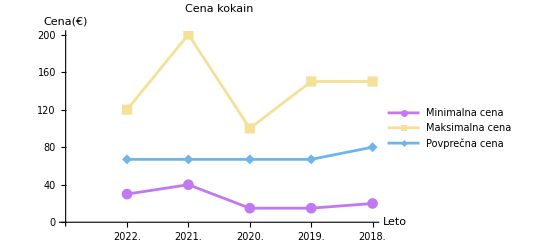

```mathematica
heroin = podatkiCENA[[1]];
letoheroin = heroin[[All,1]];
minheroin = heroin[[All, 2]];
maxheroin = heroin[[All, 3]];
povheroin = heroin[[All,4]];
grafheroin = ListLinePlot[{minheroin, maxheroin, povheroin},
AxesLabel->{"Leto", "Cena(€)"},
PlotStyle->"Pastel",
Ticks->{Thread[{Range[Length[letoheroin]], letoheroin}], Automatic},
PlotMarkers->Automatic,
PlotLegends->{"Minimalna cena", "Maksimalna cena", "Povprečna cena"},
ImageSize->400,
PlotLabel->"Cena heroina"];

kokain = podatkiCENA[[2]];
letokokain = kokain[[All,1]];
minkokain = kokain[[All, 2]];
maxkokain = kokain[[All, 3]];
povkokain = kokain[[All,4]];
grafkokain = ListLinePlot[{minkokain, maxkokain, povkokain},
AxesLabel->{"Leto", "Cena(€)"},
PlotStyle->"Pastel",
Ticks->{Thread[{Range[Length[letokokain]], letokokain}], Automatic},
PlotMarkers->Automatic,
PlotLegends->{"Minimalna cena", "Maksimalna cena", "Povprečna cena"},
ImageSize->400,
PlotLabel->"Cena kokain"];

MDMAekstazi = podatkiCENA[[3]];
letoMDMAekstazi = MDMAekstazi[[All,1]];
minMDMAekstazi = MDMAekstazi[[All, 2]];
maxMDMAekstazi= MDMAekstazi[[All, 3]];
povMDMAekstazi = MDMAekstazi[[All,4]];
grafMDMA= ListLinePlot[{minMDMAekstazi, maxMDMAekstazi, povMDMAekstazi},
AxesLabel->{"Leto", "Cena(€)"},
PlotStyle->"Pastel",
Ticks->{Thread[{Range[Length[letoMDMAekstazi]], letoMDMAekstazi}], Automatic},
PlotMarkers->Automatic,
PlotLegends->{"Minimalna cena", "Maksimalna cena", "Povprečna cena"},
ImageSize->400,
PlotLabel->"Cena MDMA/ekstazi"];

MDMAkristali= podatkiCENA[[4]];
letoMDMAkristali = MDMAkristali[[All,1]];
minMDMAkristali = MDMAkristali[[All, 2]];
maxMDMAkristali= MDMAkristali[[All, 3]];
povMDMAkristali = MDMAkristali[[All,4]];
grafMDMAkristali= ListLinePlot[{minMDMAkristali, maxMDMAkristali, povMDMAkristali},
AxesLabel->{"Leto", "Cena(€)"},
PlotStyle->"Pastel",
Ticks->{Thread[{Range[Length[letoMDMAkristali]], letoMDMAkristali}], Automatic},
PlotMarkers->Automatic,
PlotLegends->{"Minimalna cena", "Maksimalna cena", "Povprečna cena"},
ImageSize->400,
PlotLabel->"Cena MDMA kristali"];

amfetamin= podatkiCENA[[5]];
letoamfetamin = amfetamin[[All,1]];
minamfetamin = amfetamin[[All, 2]];
maxamfetamin= amfetamin[[All, 3]];
povamfetamin = amfetamin[[All,4]];
grafamfetamin= ListLinePlot[{minamfetamin, maxamfetamin, povamfetamin},
AxesLabel->{"Leto", "Cena(€)"},
PlotStyle->"Pastel",
Ticks->{Thread[{Range[Length[letoamfetamin]], letoamfetamin}], Automatic},
PlotMarkers->Automatic,
PlotLegends->{"Minimalna cena", "Maksimalna cena", "Povprečna cena"},
ImageSize->400,
PlotLabel->"Cena amfetain"];

LSD= podatkiCENA[[6]];
letoLSD= LSD[[All,1]];
minLSD = LSD[[All, 2]];
maxLSD= LSD[[All, 3]];
povLSD = LSD[[All,4]];
grafLSD= ListLinePlot[{minLSD, maxLSD, povLSD},
AxesLabel->{"Leto", "Cena(€)"},
PlotStyle->"Pastel",
Ticks->{Thread[{Range[Length[letoLSD]], letoLSD}], Automatic},
PlotMarkers->Automatic,
PlotLegends->{"Minimalna cena", "Maksimalna cena", "Povprečna cena"},
ImageSize->400,
PlotLabel->"Cena LSD"];

ketamin= podatkiCENA[[7]];
letoketamin= LSD[[All,1]];
minketamin = LSD[[All, 2]];
maxketamin= LSD[[All, 3]];
povketamin= LSD[[All,4]];
grafketamin= ListLinePlot[{minketamin, maxketamin, povketamin},
AxesLabel->{"Leto", "Cena(€)"},
PlotStyle->"Pastel",
Ticks->{Thread[{Range[Length[letoketamin]], letoketamin}], Automatic},
PlotMarkers->Automatic,
PlotLegends->{"Minimalna cena", "Maksimalna cena", "Povprečna cena"},
ImageSize->400,
PlotLabel->"Cena ketamin"];

xanax= podatkiCENA[[8]];
letoxanax= xanax[[All,1]];
minxanax = xanax[[All, 2]];
maxxanax= xanax[[All, 3]];
povxanax = xanax[[All,4]];
grafxanax= ListLinePlot[{minxanax, maxxanax, povxanax},
AxesLabel->{"Leto", "Cena(€)"},
PlotStyle->"Pastel",
Ticks->{Thread[{Range[Length[letoxanax]], letoxanax}], Automatic},
PlotMarkers->Automatic,
PlotLegends->{"Minimalna cena", "Maksimalna cena", "Povprečna cena"},
ImageSize->400,
PlotLabel->"Cena Xanax"];

grafxanax grafLSD  grafketamin grafamfetamin grafMDMAkristali  grafMDMA grafkokain grafheroin
```

## Čistost in kakovost prepovedanih drog

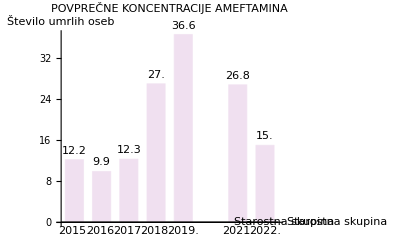
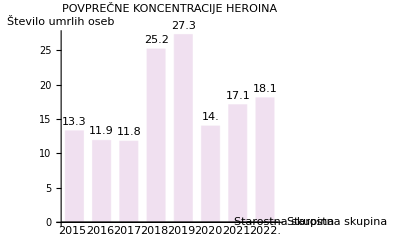
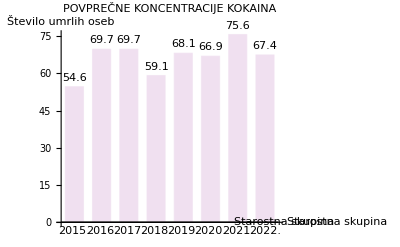
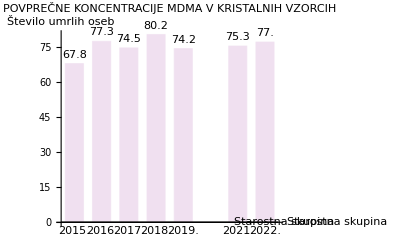
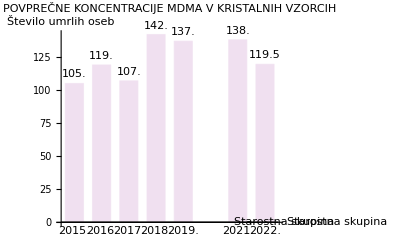

```mathematica
heroin1 = cistostInKakovot[[1]];
leto = heroin1[[All, 1]];
številoheroin = heroin1[[All, 2]];

chartheroin = BarChart[številoheroin,
ChartLabels->Placed[leto, Below],
ChartStyle->{LightPurple},
LabelingFunction->Above,
BarSpacing->0.5,
AxesLabel->{"Starostna skupina", "Število umrlih oseb"},
ImageSize->400,
PlotLabel->Style["POVPREČNE KONCENTRACIJE HEROINA", Black, Bold]
];

kokain1 = cistostInKakovot[[2]];
številokokain = kokain1[[All, 2]];

chartkokain = BarChart[številokokain,
ChartLabels->Placed[leto, Below],
ChartStyle->{LightPurple},
LabelingFunction->Above,
BarSpacing->0.5,
AxesLabel->{"Starostna skupina", "Število umrlih oseb"},
ImageSize->400,
PlotLabel->Style["POVPREČNE KONCENTRACIJE KOKAINA", Black, Bold]
];

amfetamin1 = cistostInKakovot[[3]];
številoamfetamin = amfetamin1[[All, 2]];

chartamfetamin = BarChart[številoamfetamin,
ChartLabels->Placed[leto, Below],
ChartStyle->{LightPurple},
LabelingFunction->Above,
BarSpacing->0.5,
AxesLabel->{"Starostna skupina", "Število umrlih oseb"},
ImageSize->400,
PlotLabel->Style["POVPREČNE KONCENTRACIJE AMEFTAMINA", Black, Bold]
];

MDMAkristali1 = cistostInKakovot[[4]];
številoMDMAkrist = MDMAkristali1[[All, 2]];

chartMDMAkritali = BarChart[številoMDMAkrist,
ChartLabels->Placed[leto, Below],
ChartStyle->{LightPurple},
LabelingFunction->Above,
BarSpacing->0.5,
AxesLabel->{"Starostna skupina", "Število umrlih oseb"},
ImageSize->400,
PlotLabel->Style["POVPREČNE KONCENTRACIJE MDMA V KRISTALNIH VZORCIH", Black, Bold]
];

MDMAtbl1 = cistostInKakovot[[5]];
številoMDMAtbl = MDMAtbl1[[All, 2]];

chartMDMAtbl = BarChart[številoMDMAtbl,
ChartLabels->Placed[leto, Below],
ChartStyle->{LightPurple},
LabelingFunction->Above,
BarSpacing->0.5,
ImageSize-> 400,
AxesLabel->{"Starostna skupina", "Število umrlih oseb"},

PlotLabel->Style["POVPREČNE KONCENTRACIJE MDMA V KRISTALNIH VZORCIH", Black, Bold]
];

chartheroin chartkokain chartamfetamin chartMDMAkritali chartMDMAtbl
```

## Število zasegov 2012-2022

### Vsi zasege od leta 2012 do 2022

```mathematica
število = štZasegov[[1]];
Grid[število,
Frame->All,
ItemSize->{7,2},
Background->{None, {{LightPurple, None}}}
]
```

VRSTA DROGE | heroin | kokain | ekstazi/MDMA |  | amfetamin |  | bemzodiazepini | metadon | metamfetamin |  | sintetični katinoni | LSD
ENOTA | kg | kg | tbl | kg | tbl | kg | tbl | ml | kg | tbl | g | kos
2022. | 5.8 | 678.35 | 102.5 | 0.07 | 109. | 0.72 | 7451.5 | 50290.2 | 0.54 | 38. | 116.1 | 3046.6
2021. | 226.15 | 827.91 | 245350. | 123.46 | 3850.5 | 96.92 | 7672.5 | 1459.1 | 6.64 | 27. | 7.3 | 20659.5
2020. | 4.89 | 8.57 | 13029. | 0.49 | 20. | 107.81 | 8720.5 | 2122.4 | 0.08 | 977. | 0.01 | 5926.5
2019. | 758.52 | 4.06 | 9763. | 0.2 | 79. | 18.31 | 489.5 | 1884. | 9.41 | 203.5 |  | 9391.
2018. | 334.89 | 14.22 | 511. | 0.28 | 58. | 5.7 | 17736. | 2282.9 | 0.16 | 82. |  | 
2017. | 10.71 | 12.25 | 1636. | 1.21 | 312. | 6.08 | 14177. | 1201.5 | 0.03 | 137. |  | 
2016. | 47.62 | 104.61 | 499. | 0.36 | 232. | 3.11 | 5608. | 3137.8 | 0.07 | 138. |  | 
2015. | 6.47 | 2.77 | 2908. | 1.98 | 95. | 2.11 | 10503. | 2.8 | 0.41 | 324. |  | 
2014. | 4.87 | 141.99 | 218. | 0.11 | 737. | 21.39 | 5292. | 1572.9 | 0.08 | 53. |  | 
2013. | 7.65 | 3.31 | 922. | 0.85 | 307. | 15. | 14620. | 2093.7 | 0.54 | 110. |  | 
2012. | 20.34 | 26.82 | 960. | 0. | 80. | 9.28 | 3251. | 2670. | 0.05 | 43. |  |

### Količina zaseženga heroina

```mathematica
leto =število[[3;;,1]];
zasegheroin = število[[3;;, 2]];
ListLinePlot[zasegheroin -> zasegheroin,
AxesLabel->{"Leto", "Količina [kg]"},
PlotStyle->"Pastel",
Ticks->{Thread[{Range[Length[leto]], leto}], Automatic},
PlotMarkers->Automatic,
ImageSize->400
]
```

-Graphics-

### Količina zaseženega kokaina

```mathematica
zasegkokain = število[[3;;, 3]];
ListLinePlot[zasegkokain -> zasegkokain,
AxesLabel->{"Leto", "Količina [kg]"},
PlotStyle->"Pastel",
Ticks->{Thread[{Range[Length[leto]], leto}], Automatic},
PlotMarkers->Automatic,
ImageSize->400
]
```

-Graphics-

### Količina zaseženega MDMA

```mathematica
zasegMDMAtbl = število[[3;;,4]];
zasegMDMA = število[[3;;,5]];
ListLinePlot[zasegMDMAtbl -> zasegMDMAtbl ,
AxesLabel->{"Leto", "Količina [tbl]"},
PlotStyle->"Pastel",
Ticks->{Thread[{Range[Length[leto]], leto}], Automatic},
PlotMarkers->Automatic,
ImageSize->400
]
ListLinePlot[zasegMDMA -> zasegMDMA ,
AxesLabel->{"Leto", "Količina [kg]"},
PlotStyle->"Pastel",
Ticks->{Thread[{Range[Length[leto]], leto}], Automatic},
PlotMarkers->Automatic,
ImageSize->400
]
```

-Graphics-

-Graphics-

### Količina zaseženega amfetamina

```mathematica
zasegamfetamintbl = število[[3;;,6]] ;
zasegamfetamin =število[[3;;,7]];
ListLinePlot[zasegamfetamin -> zasegamfetamin ,
AxesLabel->{"Leto", "Količina [kg]"},
PlotStyle->"Pastel",
Ticks->{Thread[{Range[Length[leto]], leto}], Automatic},
PlotMarkers->Automatic,
ImageSize->400
]
ListLinePlot[zasegamfetamintbl -> zasegamfetamintbl ,
AxesLabel->{"Leto", "Količina [tbl]"},
PlotStyle->"Pastel",
Ticks->{Thread[{Range[Length[leto]], leto}], Automatic},
PlotMarkers->Automatic,
ImageSize->400
]
```

-Graphics-

-Graphics-

### Količina zaseženega bemzodiazepinia

```mathematica
zasefbemzodiazepini = število[[3;;,8]];
ListLinePlot[zasefbemzodiazepini -> zasefbemzodiazepini,
AxesLabel->{"Leto", "Količina [tbl]"},
PlotStyle->"Pastel",
Ticks->{Thread[{Range[Length[leto]], leto}], Automatic},
PlotMarkers->Automatic,
ImageSize->400
]
```

-Graphics-

### Količina zaseženega metadona

```mathematica
zasegmetadon = število[[3;;,9]];
ListLinePlot[zasegmetadon -> zasegmetadon,
AxesLabel->{"Leto", "Količina [ml]"},
PlotStyle->"Pastel",
Ticks->{Thread[{Range[Length[leto]], leto}], Automatic},
PlotMarkers->Automatic,
ImageSize->400
]
```

-Graphics-

### Količina zaseženega metafetamina

```mathematica
zasegmetamfetamintbl = število[[3;;,10]];
zasegmetamfetaminkg = število[[3;;,11]];
ListLinePlot[zasegmetamfetamintbl -> zasegmetamfetamintbl,
AxesLabel->{"Leto", "Količina [tbl]"},
PlotStyle->"Pastel",
Ticks->{Thread[{Range[Length[leto]], leto}], Automatic},
PlotMarkers->Automatic,
ImageSize->400
]
ListLinePlot[zasegmetamfetaminkg -> zasegmetamfetaminkg,
AxesLabel->{"Leto", "Količina [kg]"},
PlotStyle->"Pastel",
Ticks->{Thread[{Range[Length[leto]], leto}], Automatic},
PlotMarkers->Automatic,
ImageSize->400
]
```

-Graphics-

-Graphics-

### Količina zaseženih sintetičnih katinonov

```mathematica
zasegkatinoni = število[[3;;,12]];
ListLinePlot[zasegkatinoni -> zasegkatinoni,
AxesLabel->{"Leto", "Količina [g]"},
PlotStyle->"Pastel",
Ticks->{Thread[{Range[Length[leto]], leto}], Automatic},
PlotMarkers->Automatic,
ImageSize->400
]
```

-Graphics-

### Količina zaseženega LSD-ija

```mathematica
zasegLSD = število[[3;;,13]];
ListLinePlot[zasegLSD -> zasegLSD,
AxesLabel->{"Leto", "Količina [g]"},
PlotStyle->"Pastel",
Ticks->{Thread[{Range[Length[leto]], leto}], Automatic},
PlotMarkers->Automatic,
ImageSize->400
]
```

-Graphics-